```mathematica
Det[{{-((t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k]))),1},{-ϵ/t2+(-2 t1^2 Cos[k]+2 t1^2/t2 ϵ)/(ϵ^2-t2^2),1}}]//Simplify
```

(-t2^6+8 t1^4 ϵ^2+4 t1^2 t2^2 ϵ^2+3 t2^4 ϵ^2-4 t1^2 ϵ^4-3 t2^2 ϵ^4+ϵ^6-16 t1^4 t2 ϵ Cos[k]-4 t1^2 t2^3 ϵ Cos[k]+4 t1^2 t2 ϵ^3 Cos[k]+8 t1^4 t2^2 Cos[k]^2-t2^2 √(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2)+ϵ^2 √(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (t2^2-ϵ^2) (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k]))

```mathematica
Solve[(-t2^6+8 t1^4 ϵ^2+4 t1^2 t2^2 ϵ^2+3 t2^4 ϵ^2-4 t1^2 ϵ^4-3 t2^2 ϵ^4+ϵ^6-16 t1^4 t2 ϵ Cos[k]-4 t1^2 t2^3 ϵ Cos[k]+4 t1^2 t2 ϵ^3 Cos[k]+8 t1^4 t2^2 Cos[k]^2-t2^2 √(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2)+ϵ^2 √(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (t2^2-ϵ^2) (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k]))==0,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→-ArcCos[ϵ/t2]},{k→ArcCos[ϵ/t2]},{k→-ArcCos[(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2 t2)]},{k→ArcCos[(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2 t2)]}}

```mathematica
1/(4 t1^2 t2 (-ϵ+t2 Cos[k]))(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/.{k->-ArcCos[(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2 t2)]}
```

(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+2 ϵ^2 (2 t1^2+t2^2-ϵ^2)+√(-16 t1^4 t2^2 (ϵ-(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+2 ϵ^2 (2 t1^2+t2^2-ϵ^2))^2))/(4 t1^2 t2 (-ϵ+(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2)))

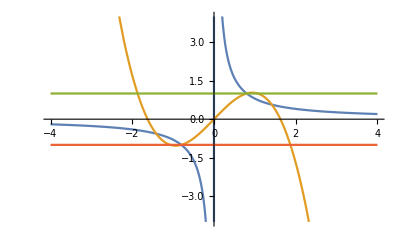

```mathematica
With[{t1=1.0,t2=0.8},Plot[{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+2 ϵ^2 (2 t1^2+t2^2-ϵ^2)+√(-16 t1^4 t2^2 (ϵ-(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+2 ϵ^2 (2 t1^2+t2^2-ϵ^2))^2))/(4 t1^2 t2 (-ϵ+(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2))),(ϵ (2 t1^2+t2^2-ϵ^2))/(2 t1^2 t2),1,-1},{ϵ,-4,4}]]
```